```mathematica
Dimensions[
```

{3,72,2}

```mathematica
list={{4,3},{2,10},{-2,25},{3,7}}
Take[#,Ordering[Last/@#,-1]]&@list
```

{{4,3},{2,10},{-2,25},{3,7}}

{{-2,25}}

```mathematica
(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]]
(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]][[1]]
(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]][[1]]
```

{-128.31,0.2116}

-220.433

-312.593

```mathematica
resultsState1={};
resultsState2={};
resultsState3={};
resultsState4={};
resultsState5={};
resultsState6={};

For[
BField:=0;, BField<1000, BField+=0.1,


(hs =Table[HOperator[StateVector[Ground]⟦i⟧,StateVector[Ground]⟦j⟧, i,j,elem,Ground,0,1/2,II[elem]]/.MagneticField-> BField,{i,Length[StateVector[Ground]]},{j,Length[StateVector[Ground]]}])//MatrixForm;
MatrixForm/@({Energies,States}=Eigensystem[hs]);
MatrixForm/@({energies = Energies[[Ordering[Energies]]],states =States[[Ordering[Energies]]]});

(ht =Table[HOperator[StateVector[D1]⟦i⟧,StateVector[D1]⟦j⟧, i,j,elem,D1,1,1/2,II[elem]]/.MagneticField-> BField,{i,Length[StateVector[D1]]},{j,Length[StateVector[D1]]}])//MatrixForm;
MatrixForm/@({EnergiesD1,StatesD1}=Eigensystem[ht]);
MatrixForm/@{energiesD1=EnergiesD1[[Ordering[EnergiesD1]]],statesD1=StatesD1[[Ordering[EnergiesD1]]]};

(hD2=Table[HOperator[StateVector[D2]⟦i⟧,StateVector[D2]⟦j⟧, i,j,elem,D2,1,3/2,II[elem]]/.MagneticField-> BField,{i,Length[StateVector[D2]]},{j,Length[StateVector[D2]]}])//MatrixForm;
MatrixForm/@({EnergiesD2,StatesD2}=Eigensystem[hD2]);
MatrixForm/@({energiesD2 =EnergiesD2[[Ordering[EnergiesD2]]],statesD2 =StatesD2[[Ordering[EnergiesD2]]]});

D1TransitionElement[i_,j_,qPolarization_]:=Quiet[Round[Sum[Sum[Select[statesD1⟦j⟧,#≠0&]⟦s⟧*Select[states⟦i⟧,#≠0&]⟦r⟧*(-1)^(-1/2+StateVector[D1]⟦Position[statesD1⟦j⟧,Select[statesD1⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧)ThreeJSymbol[{1/2,StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦1⟧},{1,qPolarization},{1/2,-StateVector[D1]⟦Position[statesD1⟦j⟧,Select[statesD1⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧}]*KroneckerDelta[StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦2⟧,StateVector[Ground]⟦Position[statesD1⟦j⟧,Select[statesD1⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦2⟧],{r,1,Length[Select[states⟦i⟧,#≠0&]]}],{s,1,Length[Select[statesD1⟦j⟧,#≠0&]]}],0.001]];

D2TransitionElement[i_,j_,qPolarization_]:=Round[Sum[Sum[Select[statesD2⟦j⟧,#≠0&]⟦s⟧*Select[states⟦i⟧,#≠0&]⟦r⟧*(-1)^(3/2-1+StateVector[D2]⟦Position[statesD2⟦j⟧,Select[statesD2⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧)ThreeJSymbol[{1/2,StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦1⟧},{1,qPolarization},{3/2,-StateVector[D2]⟦Position[statesD2⟦j⟧,Select[statesD2⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦1⟧}]*KroneckerDelta[StateVector[Ground]⟦Position[states⟦i⟧,Select[states⟦i⟧,#≠0&]⟦r⟧]⟦1,1⟧⟧⟦2⟧,StateVector[D2]⟦Position[statesD2⟦j⟧,Select[statesD2⟦j⟧,#≠0&]⟦s⟧]⟦1,1⟧⟧⟦2⟧],{r,1,Length[Select[states⟦i⟧,#≠0&]]}],{s,1,Length[Select[statesD2⟦j⟧,#≠0&]]}],0.001];



res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,1,1},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
polarisationL=(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]];
polarisationPi=(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]];
polarisationR=(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]];

row =Join[{BField},polarisationL,polarisationPi,polarisationR];
resultsState1 = AppendTo[resultsState1, row];

res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,2,2},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
polarisationL=(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]];
polarisationPi=(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]];
polarisationR=(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]];

row =Join[{BField},polarisationL,polarisationPi,polarisationR];
resultsState2 = AppendTo[resultsState2, row];

res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,3,3},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
polarisationL=(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]];
polarisationPi=(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]];
polarisationR=(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]];

row =Join[{BField},polarisationL,polarisationPi,polarisationR];
resultsState3 = AppendTo[resultsState3, row];

res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,4,4},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
polarisationL=(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]];
polarisationPi=(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]];
polarisationR=(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]];

row =Join[{BField},polarisationL,polarisationPi,polarisationR];
resultsState4 = AppendTo[resultsState4, row];


res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,5,5},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
polarisationL=(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]];
polarisationPi=(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]];
polarisationR=(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]];

row =Join[{BField},polarisationL,polarisationPi,polarisationR];
resultsState5 = AppendTo[resultsState5, row];


res=Table[Sort[Flatten[Table[{energies[[i]]-HFA[elem,Ground]/2-energiesD2[[j]],Abs[D2TransitionElement[i,j,q]]^2},{i,6,6},{j,1,Length[StateVector[D2]]}],1]],{q,-1,1}];
polarisationL=(Take[#,Ordering[Last/@#,-1]]&@res[[1]])[[1]];
polarisationPi=(Take[#,Ordering[Last/@#,-1]]&@res[[2]])[[1]];
polarisationR=(Take[#,Ordering[Last/@#,-1]]&@res[[3]])[[1]];

row =Join[{BField},polarisationL,polarisationPi,polarisationR];
resultsState6 = AppendTo[resultsState6, row];

]
```

```mathematica
resultsState6
```

{{0,1.72032,0.148225,1.73897,0.149769,1.73897,0.076176}}

```mathematica
polarisationL
```

{22.9037,0.082944}

{0,1.72032,0.148225,1.73897,0.149769,1.73897,0.076176}

InterpolatingFunction[{{0., 999.}}, <>]

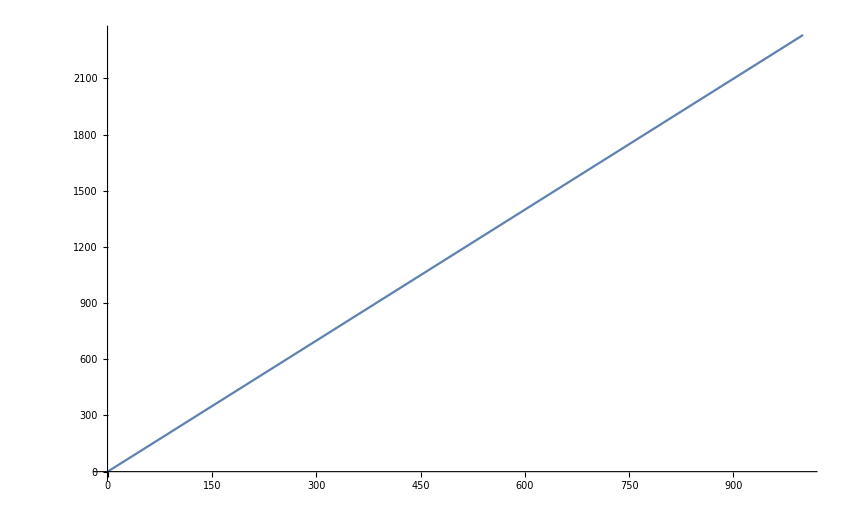

```mathematica
resultsState6[[1]]
f=Interpolation[resultsState6[[;;,1;;2]]]
Plot[f[b], {b, 0, 1000}]
```

```mathematica
f[400]
```

932.522